# TT Term Reference Value : D^0,5.02 TeV (0.5, 0.5488) (1.25, 0.3780)

## v_T=0.5,γ_c=0.39,γ_l=1.0,T=0.175(0.16-0.19)

```mathematica
TT[p_,eta_,T_]:=36*Sqrt[p^2+1.8^2]*(5*5.0676896*Pi(9*5.0676896)^2)/(2Pi)^3*2*0.39*1.0*BesselI[0,(p Sinh[eta])/T]*NIntegrate[5*(1-x)^4*BesselK[1,Cosh[eta]/T(Sqrt[0.26^2+x^2 p^2]+Sqrt[1.28^2+(1-x)^2 p^2])],{x,0,1}];
```

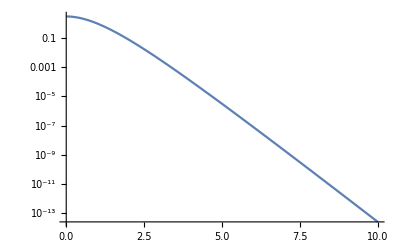

```mathematica
LogPlot[TT[p,ArcTanh[0.3],0.19],{p,0,10}]
```

```mathematica
(*5.02(0.5,   0.5488) (1.25, 0.3780)*)
(*2.76(1.5,   0.2812) (1.25, 0.3780)*)
```

```mathematica
TT[1.5,ArcTanh[0.43],0.185]
```

0.338104

```mathematica
Plot3D[TT[0.5,ArcTanh[x],y],{x,0.25,0.5},{y,0.16,0.19}]
```

-Graphics3D-

```mathematica
ArcTanh[0.25]
```

0.255413

```mathematica
Tc[p_,eta_,T_]:=BesselI[0,(p Sinh[eta])/T]*BesselK[1,(Sqrt[p^2+1.28^2]Cosh[eta])/T];
```

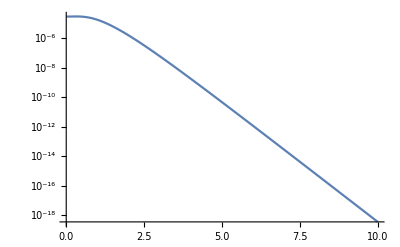

```mathematica
LogPlot[Tc[p,ArcTanh[0.5],0.155],{p,0,10}]
```